```mathematica
param1={
Subscript[k, A]->(1+μ)/2,
Subscript[k, B]->(1-μ)/2,

w1->(1-(1-(1-r)^2(1-μ^2))^(1/2))/((1-r)(1+μ)),
w2->(1+(1-(1-r)^2(1-μ^2))^(1/2))/((1-r)(1+μ))
};
```

```mathematica
Subscript[p, bulkleft][i_]:=c1 w1^i+c2 w2^i;
Subscript[p, bulkright][i_]:=d1 w1^i+d2 w2^i;
p[i_]:=Piecewise[{
{Subscript[p, left],i==1},
{Subscript[p, bulkleft][i],i≤m},
{Subscript[p, bulkright][i],i<2m},
{Subscript[p, right],i==2m}
}]
```

```mathematica
Solve[{(w1/.param1)==w1,(w2/.param1)==w2},{μ,r}]//FullSimplify
{Subscript[k, A],Subscript[k, B]}/.param1/.%//FullSimplify
```

{{μ→-1+2/(1+w1 w2),r→(-1+w1+w2-w1 w2)/(w1+w2)}}

{{1/(1+w1 w2),(w1 w2)/(1+w1 w2)}}

```mathematica
param2={
Subscript[k, A]-> 1/(1+w1 w2),
Subscript[k, B]-> (w1 w2)/(1+w1 w2),

μ-> -1+2/(1+w1 w2),
r-> (-1+w1+w2-w1 w2)/(w1+w2)
};
```

```mathematica
Solve[(1-r)Subscript[k, B] /w-1+(1-r)Subscript[k, A] w==0,{w}]//FullSimplify
```

{{w→(-1+√(1-4 (-1+r)^2 k_A k_B))/(2 (-1+r) k_A)},{w→-(1+√(1-4 (-1+r)^2 k_A k_B))/(2 (-1+r) k_A)}}

```mathematica
(* sanity check *)
(1-r)Subscript[k, B] Subscript[p, bulkleft][i-1]-Subscript[p, bulkleft][i]+(1-r)Subscript[k, A] Subscript[p, bulkleft][i+1]/.param1//Simplify
(1-r)Subscript[k, B] Subscript[p, bulkleft][i-1]-Subscript[p, bulkleft][i]+(1-r)Subscript[k, A] Subscript[p, bulkleft][i+1]/.param2//Simplify
```

0

0

```mathematica
eqs={
((1-r)(1-ϵ Subscript[k, B])-1)Subscript[p, left]+(1-r) Subscript[k, A]  Subscript[p, bulkleft][2]==0,
(1-r)ϵ Subscript[k, B] Subscript[p, left] - Subscript[p, bulkleft][2]+(1-r) Subscript[k, A] Subscript[p, bulkleft][3]==0,

(1-r)Subscript[k, B] Subscript[p, bulkleft][m-1]-Subscript[p, bulkleft][m]+(1-r)Subscript[k, A] Subscript[p, bulkright][m+1]==-r/2,
(1-r)Subscript[k, B] Subscript[p, bulkleft][m]-Subscript[p, bulkright][m+1]+(1-r)Subscript[k, A] Subscript[p, bulkright][m+2]==-r/2,

(1-r)Subscript[k, B] Subscript[p, bulkright][2m-2]-Subscript[p, bulkright][2m-1]+(1-r)ϵ Subscript[k, A] Subscript[p, right]==0,
(1-r)Subscript[k, B] Subscript[p, bulkright][2m-1]+((1-r)(1-ϵ Subscript[k, A])-1)Subscript[p, right]==0
}//Simplify;
eqs/.param2//FullSimplify
```

{(c1 w1^2+c2 w2^2-(-1+w1+w2+w1 w2 (-1+ϵ)) p_left)/(w1+w2)==0,(w1 w2 (c1 w1+c2 w2-ϵ p_left))/(w1+w2)==0,(1-w2+2 (c2-d2) w2^(1+m)+w1 (-1+2 (c1-d1) w1^m+w2))/(w1+w2)==0,(-1+w1+w2+w1 w2 (-1+2 (c1-d1) w1^m+2 (c2-d2) w2^m))/(w1+w2)==0,(d1 w1^(2 m)+d2 w2^(2 m)-ϵ p_right)/(w1+w2)==0,(d1 w1^(2 m) w2+d2 w1 w2^(2 m)+((-1+w1) (-1+w2)-ϵ) p_right)/(w1+w2)==0}

```mathematica
sol=Solve[FullSimplify[eqs/.param2],{Subscript[p, left],Subscript[p, right],c1,c2,d1,d2}];
(* unique solution *)
sol=sol[[1]];
sol=FullSimplify[sol]
```

{p_left→(w1^m (1+w1) (-1+w2) w2 (-1+w1+ϵ)-(-1+w1) w1 w2^m (1+w2) (-1+w2+ϵ))/(2 (-w1^(2 m) w2 (1+w2 (-1+ϵ)) (-1+w1+ϵ)+w1 w2^(2 m) (1+w1 (-1+ϵ)) (-1+w2+ϵ))),p_right→(w1^m w2^m ((1+w1) (-1+w2) w2^m (1+w1 (-1+ϵ))-(-1+w1) w1^m (1+w2) (1+w2 (-1+ϵ))))/(2 (-w1^(2 m) w2 (1+w2 (-1+ϵ)) (-1+w1+ϵ)+w1 w2^(2 m) (1+w1 (-1+ϵ)) (-1+w2+ϵ))),c1→((-1+w1) (1+w2 (-1+ϵ)) (w1^m (1+w1) (-1+w2) w2 (-1+w1+ϵ)-(-1+w1) w1 w2^m (1+w2) (-1+w2+ϵ)))/(2 w1 (w1-w2) (-w1^(2 m) w2 (1+w2 (-1+ϵ)) (-1+w1+ϵ)+w1 w2^(2 m) (1+w1 (-1+ϵ)) (-1+w2+ϵ))),c2→-(((-1+w2) (1+w1 (-1+ϵ)) (w1^m (1+w1) (-1+w2) w2 (-1+w1+ϵ)-(-1+w1) w1 w2^m (1+w2) (-1+w2+ϵ)))/(2 (w1-w2) w2 (-w1^(2 m) w2 (1+w2 (-1+ϵ)) (-1+w1+ϵ)+w1 w2^(2 m) (1+w1 (-1+ϵ)) (-1+w2+ϵ)))),d1→((-1+w1) w1^-m w2^m (-((1+w1) (-1+w2) w2^m (1+w1 (-1+ϵ)))+(-1+w1) w1^m (1+w2) (1+w2 (-1+ϵ))) (-1+w2+ϵ))/(2 (w1-w2) (w1^(2 m) w2 (1+w2 (-1+ϵ)) (-1+w1+ϵ)-w1 w2^(2 m) (1+w1 (-1+ϵ)) (-1+w2+ϵ))),d2→(w1^m (-1+w2) w2^-m (-((1+w1) (-1+w2) w2^m (1+w1 (-1+ϵ)))+(-1+w1) w1^m (1+w2) (1+w2 (-1+ϵ))) (-1+w1+ϵ))/(2 (w1-w2) (-w1^(2 m) w2 (1+w2 (-1+ϵ)) (-1+w1+ϵ)+w1 w2^(2 m) (1+w1 (-1+ϵ)) (-1+w2+ϵ)))}

```mathematica
(Subscript[p, left]+Sum[Subscript[p, bulkleft][i],{i,2,m}]+Sum[Subscript[p, bulkright][i],{i,m+1,2m-1}]+Subscript[p, right])/.sol//Simplify
```

1

```mathematica
q=(Sum[Subscript[p, bulkright][i],{i,m+1,2m-1}]+Subscript[p, right])/.sol;
q=FullSimplify[q]
```

-(((-1+w1) w1^(2 m) w2 (1+w2) (1+w2 (-1+ϵ)) (-1+w1+ϵ)+w1 (1+w1) (-1+w2) w2^(2 m) (1+w1 (-1+ϵ)) (-1+w2+ϵ)-w1^m w2^m (-1+w1 w2) (-((-1+w1) (-1+w2) (w1+w2))+(-1+w1) (-1+w2) (w1+w2) ϵ+2 w1 w2 ϵ^2))/(2 (w1-w2) (-w1^(2 m) w2 (1+w2 (-1+ϵ)) (-1+w1+ϵ)+w1 w2^(2 m) (1+w1 (-1+ϵ)) (-1+w2+ϵ))))

```mathematica
(* cherche eps optimal *)
epsopt=FullSimplify[Solve[Simplify[D[q,ϵ]]==0,ϵ]]
```

{{ϵ→(w1^-m w2^-m ((-1+w1) w1^m (-1+w2) w2^m (-1+w1 w2) (w1^m w2-w1 w2^m)^2+√(-((-1+w1) w1^(1+2 m) (-1+w2) w2^(1+2 m) (-1+w1 w2)^2 (w1^m-w2^m) (w1^(3 m) (1+w1) w2^2 (1+w2)-w1^2 (1+w1) w2^(3 m) (1+w2)-w1^(2 m) w2^(1+m) (2 w1+w2+w1 (7+2 w1) w2+(-1+w1) w2^2)+w1^(1+m) w2^(2 m) (w1+w1^2 (-1+w2)+2 w2+w1 w2 (7+2 w2)))))))/((-1+w1 w2) (w1^2 w2^(2 m) (1+w1 (-1+w2)+w2)+w1^(2 m) w2^2 (1+w1+(-1+w1) w2)-2 w1^(1+m) w2^(1+m) (1+w1 w2)))},{ϵ→(w1^-m w2^-m ((-1+w1) w1^m (-1+w2) w2^m (-1+w1 w2) (w1^m w2-w1 w2^m)^2-√(-((-1+w1) w1^(1+2 m) (-1+w2) w2^(1+2 m) (-1+w1 w2)^2 (w1^m-w2^m) (w1^(3 m) (1+w1) w2^2 (1+w2)-w1^2 (1+w1) w2^(3 m) (1+w2)-w1^(2 m) w2^(1+m) (2 w1+w2+w1 (7+2 w1) w2+(-1+w1) w2^2)+w1^(1+m) w2^(2 m) (w1+w1^2 (-1+w2)+2 w2+w1 w2 (7+2 w2)))))))/((-1+w1 w2) (w1^2 w2^(2 m) (1+w1 (-1+w2)+w2)+w1^(2 m) w2^2 (1+w1+(-1+w1) w2)-2 w1^(1+m) w2^(1+m) (1+w1 w2)))}}

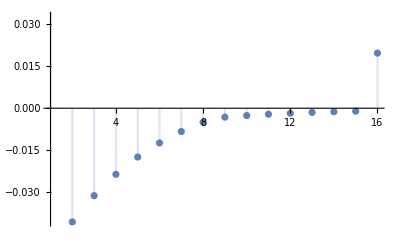
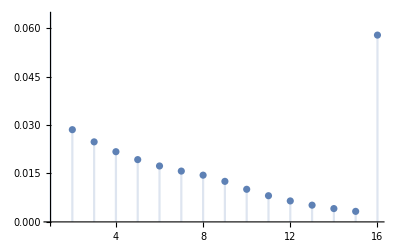

{Piecewise[{{1.1325, i==1}, {-0.0604463 0.810403^(-1+i)+0.00831129 1.0096^(-1+i), i≤8}, {-0.00367085 0.810403^(-8+i)-0.000207154 1.0096^(-8+i), i<16}, {0.0196922, i==16}, {0, True}}],Piecewise[{{0.750293, i==1}, {0.0251015 0.810403^(-1+i)+0.00815394 1.0096^(-1+i), i≤8}, {0.0159679 0.810403^(-8+i)-0.000375393 1.0096^(-8+i), i<16}, {0.0578806, i==16}, {0, True}}]}

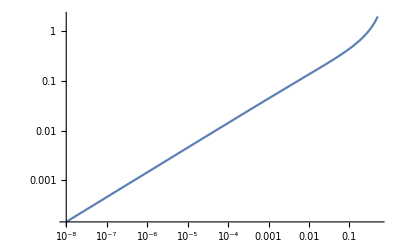

```mathematica
example={μ->0.1,r->0.001,m->8};
Table[
DiscretePlot[p[i]/.sol/.s/.param1/.example,{i,1,2m/.example}],
{s,epsopt}
]
Table[
p[i]/.sol/.s/.param1/.example,
{s, epsopt}
]
LogLogPlot[ϵ/.epsopt[[2]]/.param1/.example,{r,10^(-8),.5}]
```

```mathematica
ϵ/.epsopt[[2]]
```

(w1^-m w2^-m ((-1+w1) w1^m (-1+w2) w2^m (-1+w1 w2) (w1^m w2-w1 w2^m)^2-√(-((-1+w1) w1^(1+2 m) (-1+w2) w2^(1+2 m) (-1+w1 w2)^2 (w1^m-w2^m) (w1^(3 m) (1+w1) w2^2 (1+w2)-w1^2 (1+w1) w2^(3 m) (1+w2)-w1^(2 m) w2^(1+m) (2 w1+w2+w1 (7+2 w1) w2+(-1+w1) w2^2)+w1^(1+m) w2^(2 m) (w1+w1^2 (-1+w2)+2 w2+w1 w2 (7+2 w2)))))))/((-1+w1 w2) (w1^2 w2^(2 m) (1+w1 (-1+w2)+w2)+w1^(2 m) w2^2 (1+w1+(-1+w1) w2)-2 w1^(1+m) w2^(1+m) (1+w1 w2)))

```mathematica
w1 = Simplify[Normal[Series[w1/.param1,{r,0,2}]], 0<μ<1];
w2 = Simplify[Normal[Series[w2/.param1,{r,0,2}]], 0<μ<1];
Simplify[Series[ϵ/. epsopt[[2]],{r,0,1}], {0<μ<1, 0<r<1}]
Clear[w1,w2]
```

(√2 (1-μ)^(-1-m) (1+μ)^(3+m) √((1-μ)^(1+2 m) (1+μ)^(-7-2 m) (-1+((1-μ)/(1+μ))^m) (-(-1+μ)^2+(1-μ)^(3 m) (1+μ)^(2-3 m)+(-1+μ) ((1-μ)/(1+μ))^m (1+μ) (-3+2 μ)+(-1+μ) ((1-μ)/(1+μ))^(2 m) (1+μ) (3+2 μ))) √r)/((-1+((1-μ)/(1+μ))^m) (-1+μ+((1-μ)/(1+μ))^m+μ ((1-μ)/(1+μ))^m))+((-1+μ+((1-μ)/(1+μ))^m+μ ((1-μ)/(1+μ))^m) r)/((-1+μ) (1+μ) (-1+((1-μ)/(1+μ))^m))+O[r]^(3/2)

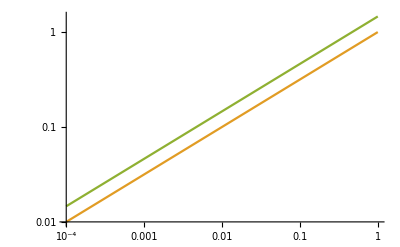

```mathematica
LogLogPlot[{
 eps/.{μ->1/4,m->12},
Sqrt[r],
Evaluate[((√2 √((1-μ^2) (1-y^m) (y^2-y^(3 m) -y^(m+1) (3-2 μ)+y^(2 m+1) (3+2 μ)))) √r)/((1-μ)^2 (1-y^m) (1-y^(m-1)))/. y-> (1-μ)/(1+μ)/.{μ->1/4,m->12}]
},{r,10^(-4),1}]
```

```mathematica
SetOptions[$Output,PageWidth->Infinity];
FortranForm[Simplify[ϵ/.epsopt[[2]]]]
```

((-1 + w1)*w1**m*(-1 + w2)*w2**m*(-1 + w1*w2)*(w1**m*w2 - w1*w2**m)**2 - Sqrt(-((-1 + w1)*w1**(1 + 2*m)*(-1 + w2)*w2**(1 + 2*m)*(-1 + w1*w2)**2*(w1**m - w2**m)*(w1**(3*m)*(1 + w1)*w2**2*(1 + w2) - w1**2*(1 + w1)*w2**(3*m)*(1 + w2) - w1**(2*m)*w2**(1 + m)*(2*w1 + w2 + w1*(7 + 2*w1)*w2 + (-1 + w1)*w2**2) + w1**(1 + m)*w2**(2*m)*(w1 + w1**2*(-1 + w2) + 2*w2 + w1*w2*(7 + 2*w2))))))/(w1**m*w2**m*(-1 + w1*w2)*(w1**2*w2**(2*m)*(1 + w1*(-1 + w2) + w2) + w1**(2*m)*w2**2*(1 + w1 + (-1 + w1)*w2) - 2*w1**(1 + m)*w2**(1 + m)*(1 + w1*w2)))

```mathematica
FortranForm[Simplify[q]]
```

-0.5*((-1 + w1)*w1**(2*m)*w2*(1 + w2)*(1 + w2*(-1 + ϵ))*(-1 + w1 + ϵ) + w1*(1 + w1)*(-1 + w2)*w2**(2*m)*(1 + w1*(-1 + ϵ))*(-1 + w2 + ϵ) - w1**m*w2**m*(-1 + w1*w2)*(-((-1 + w1)*(-1 + w2)*(w1 + w2)) + (-1 + w1)*(-1 + w2)*(w1 + w2)*ϵ + 2*w1*w2*ϵ**2))/((w1 - w2)*(-(w1**(2*m)*w2*(1 + w2*(-1 + ϵ))*(-1 + w1 + ϵ)) + w1*w2**(2*m)*(1 + w1*(-1 + ϵ))*(-1 + w2 + ϵ)))

```mathematica
FortranForm[Simplify[{w1,w2}/.param1]]
```

List((-1 + Sqrt(1 + (-1 + r)**2*(-1 + μ**2)))/((-1 + r)*(1 + μ)),-((1 + Sqrt(1 + (-1 + r)**2*(-1 + μ**2)))/((-1 + r)*(1 + μ))))

```mathematica
w1 = Simplify[Normal[Series[w1/.param1,{r,0,2}]], 0<μ<1];
w2 = Simplify[Normal[Series[w2/.param1,{r,0,2}]], 0<μ<1];
Simplify[Series[q/. epsopt[[2]],{r,0,1}], {0<μ<1, 0<r<1}]
Clear[w1,w2]
```

((1-μ)^(2 m) (1+μ)^(1-2 m))/(1+((1-μ)/(1+μ))^(2 m)+μ (-1+((1-μ)/(1+μ))^(2 m)))+(√2 (1+μ)^4 √((1-μ)^(1+2 m) (1+μ)^(-7-2 m) (-1+((1-μ)/(1+μ))^m) ((-1+((1-μ)/(1+μ))^m)^3+2 μ^3 ((1-μ)/(1+μ))^m (1+((1-μ)/(1+μ))^m)+2 μ (-1+((1-μ)/(1+μ))^m)^2 (1+((1-μ)/(1+μ))^m)+μ^2 (-1-3 ((1-μ)/(1+μ))^m+3 ((1-μ)/(1+μ))^(2 m)+((1-μ)/(1+μ))^(3 m)))) √r)/(μ (1+((1-μ)/(1+μ))^(2 m)+μ (-1+((1-μ)/(1+μ))^(2 m)))^2)-((-1+4 ((1-μ)/(1+μ))^m-9 ((1-μ)/(1+μ))^(2 m)+9 ((1-μ)/(1+μ))^(4 m)-4 ((1-μ)/(1+μ))^(5 m)+((1-μ)/(1+μ))^(6 m)+2 μ^4 ((1-μ)/(1+μ))^m (-1+((1-μ)/(1+μ))^(2 m)) (-4 m ((1-μ)/(1+μ))^m+(1+((1-μ)/(1+μ))^m)^2)+μ^2 (-1+((1-μ)/(1+μ))^(2 m)) (8 m ((1-μ)/(1+μ))^(2 m)+(1+((1-μ)/(1+μ))^m)^2 (3-8 ((1-μ)/(1+μ))^m+3 ((1-μ)/(1+μ))^(2 m)))+μ (8 m ((1-μ)/(1+μ))^(2 m) (1+((1-μ)/(1+μ))^(2 m))+(-1+((1-μ)/(1+μ))^m)^4 (3+4 ((1-μ)/(1+μ))^m+3 ((1-μ)/(1+μ))^(2 m)))+μ^3 (-8 m ((1-μ)/(1+μ))^(2 m) (1+((1-μ)/(1+μ))^(2 m))+(-1+((1-μ)/(1+μ))^m)^2 (1+6 ((1-μ)/(1+μ))^m+6 ((1-μ)/(1+μ))^(2 m)+6 ((1-μ)/(1+μ))^(3 m)+((1-μ)/(1+μ))^(4 m)))) r)/(2 (μ^2 (1+((1-μ)/(1+μ))^(2 m)+μ (-1+((1-μ)/(1+μ))^(2 m)))^3))+O[r]^(3/2)

```mathematica
((1-μ)^(2 m) (1+μ)^(1-2 m))/(1+((1-μ)/(1+μ))^(2 m)+μ (-1+((1-μ)/(1+μ))^(2 m)))==1/(1+α^(1-2m))/.{α->(1-μ)/(1+μ)}/.{μ->{1/4,1/8,1/16}}//Simplify
```

True

```mathematica
(√2 (1+μ)^4 √((-1+α^m) (1-μ)^(1+2 m) (1+μ)^(-7-2 m) ((-1+α^m)^3+2 (-1+α^m)^2 (1+α^m) μ+(-1-3 α^m+3 α^(2 m)+α^(3 m)) μ^2+2 α^m (1+α^m) μ^3)))/(μ (1+α^(2 m)+(-1+α^(2 m)) μ)^2)==(√(2(1-α^m)α^(1+2m)  (1-α^(m-1)) (1+α^(2 m-1)-2 α^(m-1) (1-μ))))/(α μ (1+α^(2 m-1))^2)  /.{α->(1-μ)/(1+μ)}/.{μ->{1/4,1/8}}//Simplify
```

True

```mathematica
Factor[1-μ+α^(2 m) (1+μ)]
```

1+α^(2 m)-μ+α^(2 m) μ

```mathematica
1/(μ (1-μ+α^(2 m) (1+μ))^2)√2 (1+μ) √((-1+α^m)α^(1+2m)  (-1+α^m+μ+α^m μ) (1-2 α^m+α^(2 m)-μ+α^(2 m) μ+2 α^m μ^2))
```

```mathematica
Factor[2(1-α^m)α^(1+2m)  (1-α^(m-1)) (1+α^(2 m-1)-2 α^(m-1) (1-μ))]
```

2 α^(-1+2 m) (-1+α^m) (-α+α^m) (α-2 α^m+α^(2 m)+2 α^m μ)